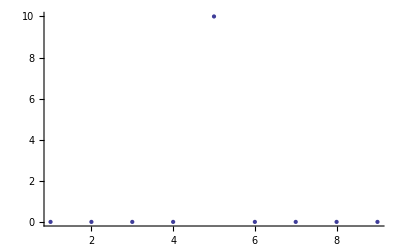
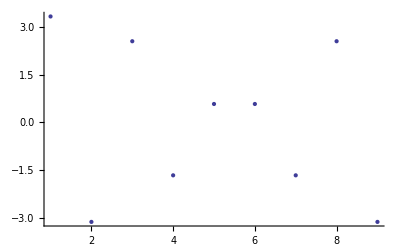
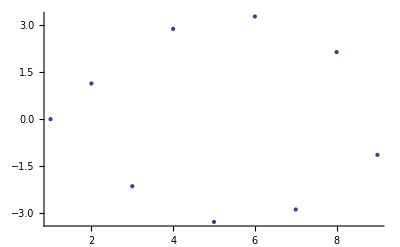
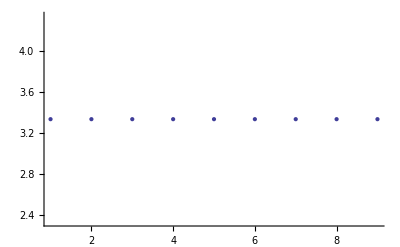
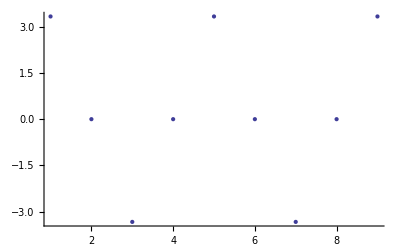
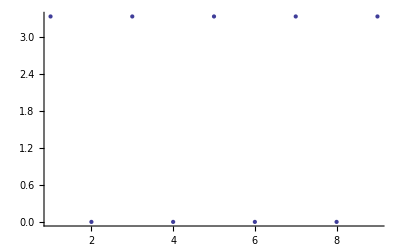
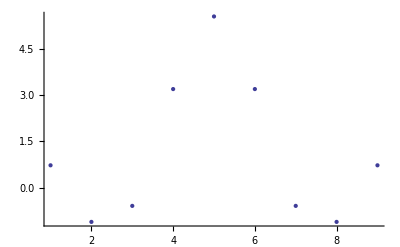
-Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Block[{list,l,flist,fclist,fslist},
list={0,0,0,0,10,0,0,0,0};
l=Length@list;
flist=Fourier[list];
fclist=FourierDCT[list];
fslist=FourierDST@list;
TableForm@{
{ListPlot@list},
{ListPlot@Re@flist,ListPlot@Im@flist,ListPlot@Abs@flist},
{ListPlot@fclist,ListPlot@Abs@fclist,ListPlot@fslist,ListPlot@Abs@fslist},
{ListPlot@FourierDCT[PadRight[Take[fclist,6],l,0],3]}
}
]
```

```mathematica
Exp[ⅈ 2π z/λ]/(ⅈ λ z)Exp[ⅈ π/(λ z)(x^2+y^2)];
FourierTransform[%,{x,y},{ξ,η},FourierParameters->{0,2π}];
Simplify@Normal@Series[%Exp[-ⅈ 2π /λ z],{λ ,0,2}] Exp[ⅈ 2π /λ z]
InverseFourierTransform[%,{ξ,η},{x,y},FourierParameters->{0,2π}]
```

ⅇ^((2 ⅈ π z)/λ) (1-ⅈ π z λ (η^2+ξ^2)-1/2 π^2 z^2 λ^2 (η^2+ξ^2)^2)

0